# Powerplay

Evolutionary powerplay for Nascence materials

This example contains a search for classifiers

```mathematica
Row[{Style["Jan Koutnik, IDSIA, E-mail:  ",FontFamily->"Roman",FontSize->16],DynamicModule[{r="@"->".",bt,b=Button[bt,b=Hyperlink["mailto:"~~StringReplace[bt,{r,Reverse@r}]]]},bt="hkou.idsia@ch";Dynamic@b]}]
```

Jan Koutnik, IDSIA, E-mail:

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/koutnij/Dropbox/math/nascence

```mathematica
LaunchKernels[2]
```

{KernelObject[1,local],KernelObject[2,local]}

## Imports

```mathematica
Import["../libMLP/bp9.m"]
```

```mathematica
Import["../libNES/nes10.m"]
```

```mathematica
Import["../libCoSyNE/libCosyne9.m"]
```

## VM

Vitual material is a simple MLP here :

```mathematica
actF=Tanh;
```

```mathematica
vm=randomNet[{20,500,500,1}];
```

```mathematica
evalVM[vm_,x_]:=Last@fwdPass[vm,x]
```

```mathematica
res=Sort@Flatten[evalVM[vm,#]&/@RandomReal[{-1,1},{500,20}]];
Min@res
Max@res
```

-1.

1.

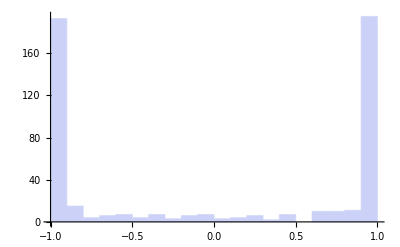

```mathematica
Histogram[res,20]
```

```mathematica
evalVM[vm_,config_,input_]:=evalVM[vm,Join[config,input]]
```

```mathematica
plotBounds[vm_,config_,set_]:=With[{points=(First/@#)&/@SortBy[GatherBy[set,Last],#⟦1,2,1⟧&]},Show[{
ContourPlot[Sign@First@evalVM[vm,config,{x,y}],{x,-1,1},{y,-1,1},Contours->{0},ContourShading->{LightRed,LightGreen},ContourStyle->Directive[Black,Dashed],FrameTicks->False,ImageSize->100],
ListPlot[points,PlotStyle->{Darker@Red,Darker@Green}]
}]]
```

## Powerplay Example - 2-space Classifiers

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/koutnij/Dropbox/math/nascence

In this example a space of classifiers is explored.

```mathematica
maxTasks=1000;
```

```mathematica
SeedRandom[30];
taskSet=RandomReal[{-1,1},{maxTasks,2}];
```

```mathematica
fitFn[g_,set_]:=With[{diff=Flatten[(evalVM[vm,g,#]&/@set⟦All,1⟧)-set⟦All,2⟧]},Total[diff^2]]
```

This adds a number of non - solved tasks :

```mathematica
fitFn[g_,set_]:=With[{eval=Flatten[(evalVM[vm,g,#]&/@set⟦All,1⟧)]},Mean[(eval-Flatten@set⟦All,2⟧)^2]+Length[set]-Count[MapThread[Equal,{Sign@eval,Flatten@set⟦All,2⟧}],True]]
```

```mathematica
fitFn[g_]:=fitFn[g,trainingSet]
```

```mathematica
solvesAllTasksQ[g_,set_]:=Equal[Sign@Flatten[(evalVM[vm,g,#]&/@set⟦All,1⟧)],Flatten@set⟦All,2⟧]
```

```mathematica
solvesAllTasksQ[g_]:=solvesAllTasksQ[g,trainingSet]
```

```mathematica
optimize[pop_,fitFn_,trainingSet_,nGen_]:=Module[{popTmp},NestWhile[(popTmp=coSyNEstep[#,fitFn[#,trainingSet]&,minimize->True,mutate->0.8,permuteAll->True,verbose->False,elite->1];Print[{popTmp⟦1,1⟧,solvesAllTasksQ[popTmp⟦1,2⟧,trainingSet]}];popTmp)&,pop,Not[solvesAllTasksQ[#⟦1,2⟧,trainingSet]]&,1,
nGen]]
```

```mathematica
reevaluate[pop_,fitFn_]:=SortBy[{fitFn[#],#}&/@pop⟦All,2⟧,First]
```

```mathematica
appendTask[set_,config_]:=With[{point=taskSet⟦Length[set]+1⟧},Append[set,{point,-Sign[evalVM[vm,config,point]]}]]
```

```mathematica
powerplay[fitFn_,popSize_,nGen_,nTasks_]:=Module[{pop,set},
set={{taskSet⟦1⟧,{1}}};(*first task*)
pop=SortBy[newRandomPop[popSize,dim,NormalDistribution[0,1],fitFn[#,set]&],First];
Print["Generated population"];
Nest[
(Print["# of tasks : "<>ToString@Length[set]];
pop=optimize[pop,fitFn,set,nGen];(*optimize*)
Print@plotBounds[vm,pop⟦1,2⟧,set];
set=appendTask[set,pop⟦1,2⟧];(*add next task*)
pop=reevaluate[pop,fitFn[#,set]&];
pop)&
,pop,nTasks]
]
```

## Example Experiment

Powerplay with population size of 8, 30 generations of CoSyNE and 10 consecutive classification tasks to solve :

```mathematica
nInputs=20;dim=nInputs-2;
```

```mathematica
vm=randomNet[{nInputs,500,500,1}];
```

```mathematica
pop=powerplay[fitFn,32,300,10];
```

Generated population

# of tasks : 1

-Graphics-

# of tasks : 2

-Graphics-

# of tasks : 3

{0.383239,True}

-Graphics-

# of tasks : 4

$Aborted